### generate all the tuples:

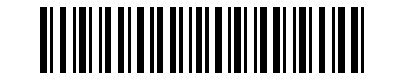

```mathematica
ArrayPlot[{BitXor @@@ IntegerDigits[Range[0,100],2]}]
```

```mathematica
BitXor @@@ IntegerDigits[Range[0,100],2]
```

{0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1}

```mathematica
training=Join[#, If[BitXor @@ #==1,{1,1,1,1,1},{0,0,0,0,0}]]& /@   Tuples[{0,1},5];
```

```mathematica
ArrayPlot[training]
```

-Graphics-

```mathematica
ToStringList[x_] := StringJoin[Riffle[Map[ToString,x, {2}], "\n"]]
```

```mathematica
Export["parity-training.txt",ToStringList[training],"Lines"]
```

parity-training.txt

```mathematica
questions=Table["?",{5}];
testing=Join[#, questions]& /@   Tuples[{0,1},5];
```

```mathematica
Export["Tuples-10.txt",ToStringList[Tuples[{0,1},10]],"Lines"]
```

Tuples-10.txt

```mathematica
Export["parity-testing.txt",ToStringList[testing],"Lines"]
```

parity-testing.txt

```mathematica
ImportTxt[file_] := ReplaceAll[Characters/@Import[file,"Lines"],{"0"->0,"1"->1,"?"->0.5}];
```

```mathematica
ImportFloat[file_]:=Import[file,"TSV"];
```

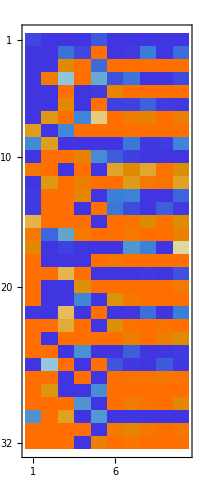

```mathematica
MatrixPlot @ ImportFloat["parity-output.tsv"]
```

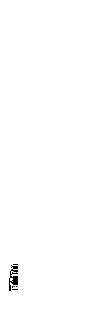
-Graphics--Graphics-

```mathematica
Row[{ArrayPlot[
ImportTxt["parity-output.txt"],PixelConstrained->10],ArrayPlot[training,PixelConstrained->10]}]
```